Test parameters

```mathematica
β=10;
K=7;
J = 9;
Q = 4;
λ1 = 1;
Λ2 = 10;
nIter = 11;
tauTest = 1/4;
```

## 1. Define Hamiltonian

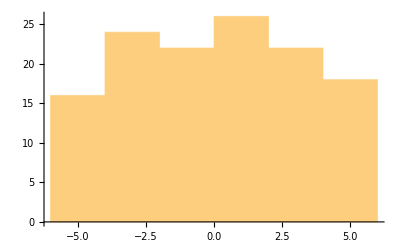

```mathematica
SeedRandom[0];
ℕ=2*K;
cr = {{0, 1}, {0, 0}}; 
an ={{0, 0}, {1, 0}};
id = IdentityMatrix[2];
id2 = {{-1, 0}, {0, 1}};
c[n_] := SparseArray[KroneckerProduct @@ (Table[id, {n-1}]~Join~{cr}~Join~Table[id2,{K-n}])]
cd[n_] := SparseArray[KroneckerProduct @@ (Table[id, {n-1}]~Join~{an}~Join~Table[id2,{K-n}])]
Do[ψ[n]=1/(√2)(c[n]+cd[n]), {n,K}];
Do[ψ[K+n]=1/(√2)(-I c[n]+I cd[n]), {n, K}];
Do[ψ2[i1,i2]=ψ[i1].ψ[i2], {i1, ℕ}, {i2,i1+1,ℕ}];
Do[ψ4[i1,i2,i3,i4] = ψ2[i1,i2].ψ2[i3,i4], {i1, ℕ}, {i2, i1+1, ℕ}, {i3, i2+1, ℕ}, {i4, i3+1, ℕ}];
js = RandomVariate[NormalDistribution[0,√(J^2 ((Q-1)!)/ℕ^(Q-1))],{ℕ, ℕ, ℕ, ℕ}, WorkingPrecision -> 100];
H= I^(Q/2) Sum[js[[i1,i2,i3,i4]] ψ4[i1, i2, i3, i4], {i1, ℕ}, {i2, i1+1, ℕ}, {i3, i2+1, ℕ}, {i4, i3+1, ℕ}]//Normal;
iv = H//N//Eigenvalues//Sort;
iv//Histogram
```

```mathematica
|
```

## 2. Define and simulate finite-N propagator

, where  if   and  if .

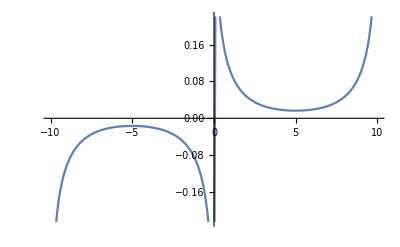

```mathematica
H = H//N;
Clear[Gn];
Gn[a_,b_,τ_,β_,λ_] := Gn[a,b,τ,β,λ] = Block[{},
If[τ>0,
Eτ = MatrixExp[-τ H λ];
Eβτ = MatrixExp[(-β+τ)H λ];
Tr[Eβτ.ψ[a].Eτ.ψ[b]]/Tr[Eβτ.Eτ],
Eτ = MatrixExp[+τ H λ];
Eβτ = MatrixExp[(-β-τ)H λ];
-Tr[Eβτ.ψ[b].Eτ.ψ[a]]/Tr[Eβτ.Eτ],
]
]
Dynamic[tt]
tbGweak = Table[{tt,Gn[1,1,tt,β,λ1]}, {tt,-β,β,1/10}]//Re;
lp = {tbGweak}//ListPlot[#, Joined->True]&
```

## 3. Define and simulate large-N (Schwinger-Dyson) propagator

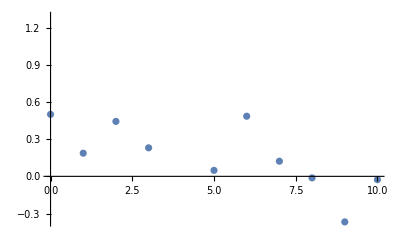

```mathematica
slω =ω -> (2π)/β(n+1/2);
sln = n -> (ω β)/(2π)-1/2;
Clear[G, Σ, Gτ]; 
Σ[0,n_]=0;
G[i_, nn_] := -1/(I ω + Σ[i, nn]) /.slω /.n ->nn;
Gτ[i_,τ_?NumericQ] := Gτ[i,τ]=1/2 Sign[τ]+1/β Sum[Exp[-I ω τ/.slω] (G[i,n]-G[0,n])//N, {n, -Λ2,Λ2}]
Σ[i_,nn_] := Σ[i,nn] = NIntegrate[J^2 Gτ[i-1,τ]^(Q-1) Exp[I ω τ  /.slω] /.n->nn, {τ, -β/2, β/2}]
Table[{n, Gτ[n,tauTest]}, {n,0,10}]//Re//ListPlot
```

## 4. Plot them against each other

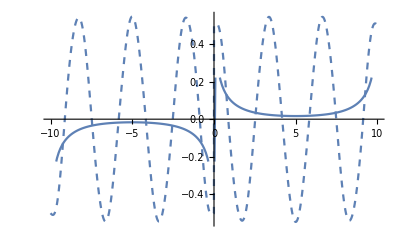

```mathematica
Show[Plot[Gτ[nIter,t]//Re, {t,-β,β}, PlotStyle->Dashed],lp]
```